# Big Data Driven Perovskite Solar Cell Stability Analysis

```mathematica
1. Import data
```

Import data from “path/data.csv”

```mathematica
data=Import["D:/Github/PSCstability/datam.csv"];(*Fill in the path first*)
```

Definition of the data index function Index[i,str] with i for row number and str for column title

```mathematica
Index[i_,str_]:=data⟦i,Position[data⟦1,All⟧,str]⟦1,1⟧⟧
```

```mathematica
2. Calculation  of TS80m and tolrance  factor
```

```mathematica
Efficiency  values
```

```mathematica
jvefficiency=Table[If[(Index[i,"JV_light_intensity"]==100)~And~(Index[i,"JV_default_PCE"]≠"")~And~(Index[i,"JV_default_PCE"]≠0),Index[i,"JV_default_PCE"],-1],{i,2,7420}];
```

```mathematica
initialefficiency=Table[Which[(Index[i,"Stability_PCE_initial_value"]≠"")~And~(Index[i,"Stability_PCE_initial_value"]≠100),Index[i,"Stability_PCE_initial_value"],Index[i,"JV_default_PCE"]≠"",Index[i,"JV_default_PCE"],True,-1],{i,2,7420}];
```

Calculation of TS80m (ts80mod) values

```mathematica
ts80=Table[Which[(Index[i,"Stability_PCE_end_of_experiment"]≥99)~Or~(Index[i,"Stability_PCE_end_of_experiment"]==""),-1,Index[i,"Stability_PCE_burn_in_observed"]=="TRUE",Which[Index[i,"Stability_PCE_Ts80"]≠"",Index[i,"Stability_PCE_Ts80"],Index[i,"Stability_PCE_Tse80"]≠"",Index[i,"Stability_PCE_Tse80"],(Index[i,"Stability_PCE_T80"]≠"")~And~(Index[i,"Stability_time_total_exposure"]≠Index[i,"Stability_PCE_T80"])~And~(Index[i,"Stability_PCE_end_of_experiment"]≠80)~And~(Index[i,"Stability_PCE_end_of_experiment"]≠0),((Index[i,"Stability_time_total_exposure"]-Index[i,"Stability_PCE_T80"])*Log[0.8])/(Log[Index[i,"Stability_PCE_end_of_experiment"]]-Log[80]),(Index[i,"Stability_PCE_after_1000_h"]≠"")~And~(Index[i,"Stability_time_total_exposure"]≠1000)~And~(Index[i,"Stability_PCE_end_of_experiment"]≠Index[i,"Stability_PCE_after_1000_h"])~And~(Index[i,"Stability_PCE_end_of_experiment"]≠0),((Index[i,"Stability_time_total_exposure"]-1000)*Log[0.8])/(Log@Index[i,"Stability_PCE_end_of_experiment"]-Log@Index[i,"Stability_PCE_after_1000_h"]),Index[i,"Stability_PCE_T80"]≠"",Index[i,"Stability_PCE_T80"],Index[i,"Stability_PCE_Te80"]≠"",Index[i,"Stability_PCE_Te80"],Index[i,"Stability_PCE_end_of_experiment"]≠0,(Index[i,"Stability_time_total_exposure"]*Log[0.8])/(Log@Index[i,"Stability_PCE_end_of_experiment"]-Log[100]),True,-1],Index[i,"Stability_PCE_burn_in_observed"]=="FALSE",Which[Index[i,"Stability_PCE_T80"]≠"",Index[i,"Stability_PCE_T80"],Index[i,"Stability_PCE_Te80"]≠"",Index[i,"Stability_PCE_Te80"],Index[i,"Stability_PCE_end_of_experiment"]≠0,(Index[i,"Stability_time_total_exposure"]*Log[0.8])/(Log@Index[i,"Stability_PCE_end_of_experiment"]-Log[100]),Index[i,"Stability_PCE_Ts80"]≠"",Index[i,"Stability_PCE_Ts80"],Index[i,"Stability_PCE_Tse80"]≠"",Index[i,"Stability_PCE_Tse80"],True,-1]],{i,2,7420}]/.(x_/;x<=0->"");
temperature1=Table[StringCases[Index[i,"Stability_temperature_range"],x:NumberString~~"; "->x],{i,2,7420}];
temperature2=Table[StringCases[Index[i,"Stability_temperature_range"],"; "~~x:NumberString->x],{i,2,7420}];
temperature=Flatten@Table[Which[(temperature1⟦i⟧≠{})~And~(temperature2⟦i⟧≠{}),ToExpression@ToString[0.5*(temperature1⟦i⟧+temperature2⟦i⟧)],(temperature1⟦i⟧=={})~And~(temperature2⟦i⟧=={}),25,True,DeleteCases[{temperature1⟦i⟧,temperature2⟦i⟧},{}]],{i,1,7419}];
AFt=Table[(E^(-0.6/(8.6*10^-5*ToExpression@ToString[(temperature⟦i⟧+273)])))/(E^(-0.6/(8.6*10^-5*300))),{i,1,7419}];
humidity=Table[Which[Index[i,"Stability_relative_humidity_average_value"]≠"",Index[i,"Stability_relative_humidity_average_value"],(Index[i,"Stability_atmosphere"]=="Air")~Or~(Index[i,"Stability_atmosphere"]=="Ambient"),40,Index[i,"Stability_atmosphere"]=="Water",100,True,0],{i,2,7420}];
AFh=Table[If[humidity⟦i⟧≤20,1,ToExpression@ToString[humidity⟦i⟧*0.05]],{i,1,7419}];
illumination=Table[Which[Index[i,"Stability_light_intensity"]≠"",Index[i,"Stability_light_intensity"],(Index[i,"Stability_light_source_type"]=="Indoor light"),30,(Index[i,"Stability_light_source_type"]=="UV lamp"),5,Index[i,"Stability_light_source_type"]=="Tungsten",50,True,100],{i,2,7420}];
AFi=Table[If[illumination⟦i⟧≤10,0.1^0.7,(ToExpression@ToString[illumination⟦i⟧*0.01])^0.7],{i,1,7419}];
ts80mod=Table[If[ToString@ts80⟦i⟧≠"",ToExpression@ToString[ts80⟦i⟧*AFt⟦i⟧*AFh⟦i⟧*AFi⟦i⟧],""],{i,1,7419}];
ts80raw=Table[If[ToString@ts80⟦i⟧≠"",ToExpression@ToString[ts80⟦i⟧],""],{i,1,7419}];
AFtvalues=Table[If[ToString@ts80⟦i⟧≠"",ToExpression@ToString[AFt⟦i⟧],""],{i,1,7419}];
AFhvalues=Table[If[ToString@ts80⟦i⟧≠"",ToExpression@ToString[AFh⟦i⟧],""],{i,1,7419}];
AFivalues=Table[If[ToString@ts80⟦i⟧≠"",ToExpression@ToString[AFi⟦i⟧],""],{i,1,7419}];
```

Calculation of tolrance factors

```mathematica
Acationstemp=Table[If[(Index[i,"Perovskite_dimension_list_of_layers"]==3)~Or~(StringQ[Index[i,"Perovskite_dimension_list_of_layers"]]~And~StringContainsQ[Index[i,"Perovskite_dimension_list_of_layers"],"3"])~And~(Index[i,"Encapsulation"]=="FALSE"),StringSplit[If[StringContainsQ[Index[i,"Perovskite_composition_a_ions"],"|"],StringTake[Index[i,"Perovskite_composition_a_ions"],StringPosition[Index[i,"Perovskite_composition_a_ions"],"|"]⟦1,1⟧-1],Index[i,"Perovskite_composition_a_ions"]],{"; "," "}],{"None"}],{i,2,7420}];
Acations=Table[If[(Union[Acationstemp⟦i⟧,{"Cs","FA","MA"}]=={"Cs","FA","MA"})~And~(Acationstemp⟦i⟧≠{}),Acationstemp⟦i⟧,{"None"}],{i,1,7419}];
Astoitemp=Table[If[Acations⟦i-1⟧≠{"None"},Index[i,"Perovskite_composition_a_ions_coefficients"],0],{i,2,7420}];
Astoi=Table[If[StringQ[Astoitemp⟦i⟧],StringSplit[If[StringContainsQ[Astoitemp⟦i⟧,"|"],StringTake[Astoitemp⟦i⟧,StringPosition[Astoitemp⟦i⟧,"|"]⟦1,1⟧-1],Astoitemp⟦i⟧],{"; "," "}],Astoitemp⟦i⟧],{i,1,7419}]/.{{}->0,{"x"}->0,0.005->{"0.005"},0.85->{"0.85"},0.98->{"0.98"},1->{"1"},2->{"2"},3->{"3"}};
A=N@Table[If[(ListQ@Astoi⟦i⟧)~And~(Length@Astoi⟦i⟧==Length@Acations⟦i⟧),Total@ToExpression@ToString[(Astoi[[i]])*(Acations[[i]]/.{"Cs"->167,"FA"->253,"MA"->217})]/ToExpression@ToString@Total@Astoi[[i]],0],{i,1,7419}];
Bcationstemp=Table[If[(Index[i,"Perovskite_dimension_list_of_layers"]==3)~Or~(StringQ[Index[i,"Perovskite_dimension_list_of_layers"]]~And~StringContainsQ[Index[i,"Perovskite_dimension_list_of_layers"],"3"])~And~(Index[i,"Encapsulation"]=="FALSE"),StringSplit[If[StringContainsQ[Index[i,"Perovskite_composition_b_ions"],"|"],StringTake[Index[i,"Perovskite_composition_b_ions"],StringPosition[Index[i,"Perovskite_composition_b_ions"],"|"]⟦1,1⟧-1],Index[i,"Perovskite_composition_b_ions"]],{"; "," "}],{"None"}],{i,2,7420}];
Bcations=Table[If[(Union[Bcationstemp⟦i⟧,{"Pb","Sn"}]=={"Pb","Sn"})~And~(Bcationstemp⟦i⟧≠{}),Bcationstemp⟦i⟧,{"None"}],{i,1,7419}];
Bstoitemp=Table[If[Bcations⟦i-1⟧≠{"None"},Index[i,"Perovskite_composition_b_ions_coefficients"],0],{i,2,7420}];
Bstoi=Table[If[StringQ[Bstoitemp⟦i⟧],StringSplit[If[StringContainsQ[Bstoitemp⟦i⟧,"|"],StringTake[Bstoitemp⟦i⟧,StringPosition[Bstoitemp⟦i⟧,"|"]⟦1,1⟧-1],Bstoitemp⟦i⟧],{"; "," "}],Bstoitemp⟦i⟧],{i,1,7419}]/.{{}->0,0.93->{"0.93"},0.95->{"0.95"},0.995->{"0.995"},1->{"1"},5->{"5"},9->{"9"}};
B=N@Table[If[(ListQ@Bstoi⟦i⟧)~And~(Length@Bstoi⟦i⟧==Length@Bcations⟦i⟧),Total@ToExpression@ToString[(Bstoi[[i]])*(Bcations[[i]]/.{"Pb"->119,"Sn"->112})]/ToExpression@ToString@Total@Bstoi[[i]],0],{i,1,7419}];
Xanionstemp=Table[If[(Index[i,"Perovskite_dimension_list_of_layers"]==3)~Or~(StringQ[Index[i,"Perovskite_dimension_list_of_layers"]]~And~StringContainsQ[Index[i,"Perovskite_dimension_list_of_layers"],"3"])~And~(Index[i,"Encapsulation"]=="FALSE"),StringSplit[If[StringContainsQ[Index[i,"Perovskite_composition_c_ions"],"|"],StringTake[Index[i,"Perovskite_composition_c_ions"],StringPosition[Index[i,"Perovskite_composition_c_ions"],"|"]⟦1,1⟧-1],Index[i,"Perovskite_composition_c_ions"]],{"; "," "}],{"None"}],{i,2,7420}];
Xanions=Table[If[(Union[Xanionstemp⟦i⟧,{"Br","Cl","I"}]=={"Br","Cl","I"})~And~(Xanionstemp⟦i⟧≠{}),Xanionstemp⟦i⟧,{"None"}],{i,1,7419}];
Xstoitemp=Table[If[Xanions⟦i-1⟧≠{"None"},Index[i,"Perovskite_composition_c_ions_coefficients"],0],{i,2,7420}];
Xstoi=Table[If[StringQ[Xstoitemp⟦i⟧],StringSplit[If[StringContainsQ[Xstoitemp⟦i⟧,"|"],StringTake[Xstoitemp⟦i⟧,StringPosition[Xstoitemp⟦i⟧,"|"]⟦1,1⟧-1],Xstoitemp⟦i⟧],{"; "," "}],Xstoitemp⟦i⟧],{i,1,7419}]/.{{}->0,{"x"}->0,0.4->{"0.4"},1->{"1"},3->{"3"},4->{"4"},5->{"5"},6->{"6"},7->{"7"},9->{"9"},10->{"10"},16->{"16"},28->{"28"}};
X=N@Table[If[(ListQ@Xstoi⟦i⟧)~And~(Length@Xstoi⟦i⟧==Length@Xanions⟦i⟧),Total@ToExpression@ToString[(Xstoi[[i]])*(Xanions[[i]]/.{"Br"->196,"Cl"->181,"I"->220})]/ToExpression@ToString@Total@Xstoi[[i]],0],{i,1,7419}];
TolFac=Table[If[(A⟦i⟧≠0)~And~(B⟦i⟧≠0)~And~(X⟦i⟧≠0),(A⟦i⟧+X⟦i⟧)/(√2*(B⟦i⟧+X⟦i⟧)),""],{i,1,7419}];
```

```mathematica
3. Statistical analysis
```

```mathematica
To give a list of most widely used compositions
```

```mathematica
tolfaclist=Sort[Table[{Union[TolFac][[i]],Count[TolFac,Union[TolFac][[i]]]},{i,1,(Dimensions@Union[TolFac])[[1]]}],#1[[2]]>#2[[2]]&][[1;;12]];
Table[{{Acations[[#]][[1]],Astoi[[#]][[1]],Bcations[[#]][[1]],Bstoi[[#]][[1]],Xanions[[#]][[1]],Xstoi[[#]][[1]]}&[Position[TolFac,tolfaclist⟦i,1⟧][[1]]],tolfaclist⟦i⟧},{i,{1}~Join~Array[2+#&,9]}]//MatrixForm
```

({{MA},{1},{Pb},{1},{I},{3}} | {0.911521,3618}
{{FA,MA},{0.85,0.15},{Pb},{1},{Br,I},{0.45,2.55}} | {0.978228,301}
{{Cs,FA,MA},{0.05,0.79,0.16},{Pb},{1},{Br,I},{0.51,2.49}} | {0.968778,273}
{{Cs},{1},{Pb},{1},{Br,I},{1,2}} | {0.809648,198}
{{Cs},{1},{Pb},{1},{Br},{3}} | {0.814856,124}
{{Cs,FA,MA},{0.05,0.81,0.14},{Pb},{1},{Br,I},{0.45,2.55}} | {0.969921,103}
{{FA},{1},{Pb},{1},{I},{3}} | {0.986612,87}
{{Cs},{1},{Pb},{1},{I},{3}} | {0.807228,70}
{{FA,MA},{0.83,0.17},{Pb},{1},{Br,I},{0.51,2.49}} | {0.977096,65}
{{FA,MA},{0.83,0.17},{Pb},{1},{Br,I},{0.51,2.49}} | {0.977096,65})

```mathematica
Calculation of arrays for heat maps
```

```mathematica
dateform=Table[StringCases[Index[i,"Ref_publication_date"],x:NumberString~~"/"~~y:NumberString~~"/"~~z:NumberString->x~~"/"~~y]⟦1⟧,{i,2,7420}];
date=Table[ToExpression@ToString@Ceiling@((#⟦1⟧-2012)*12+#⟦2⟧-8)&[StringCases[Index[i,"Ref_publication_date"],x:NumberString~~"/"~~y:NumberString~~"/"~~z:NumberString->{x,y}]⟦1⟧],{i,2,7420}];
ts80moddenplot=ConstantArray[0,{106,90}];
For[i=1,i<7420,i++,If[(ts80mod⟦i⟧≠"")~And~(TolFac⟦i⟧≠""),Which[(ts80moddenplot⟦date⟦i⟧+1,Ceiling[400*(TolFac⟦i⟧-0.8)]⟧==0),ts80moddenplot⟦date⟦i⟧+1,Ceiling[400*(TolFac⟦i⟧-0.8)]⟧=i,(ts80mod⟦i⟧>ts80mod⟦ts80moddenplot⟦date⟦i⟧+1,Ceiling[400*(TolFac⟦i⟧-0.8)]⟧⟧),ts80moddenplot⟦date⟦i⟧+1,Ceiling[400*(TolFac⟦i⟧-0.8)]⟧=i]]];
ts80modfreqplot=ConstantArray[0,{106,90}];
For[i=1,i<7420,i++,If[(ts80mod⟦i⟧≠"")~And~(TolFac⟦i⟧≠""),ts80modfreqplot⟦date⟦i⟧+1,Ceiling[400*(TolFac⟦i⟧-0.8)]⟧++]];
denplot=Join[Transpose@{{0}~Join~Table[(ToString@Floor[(i+6)/12+2012]~~"/"~~ToString[Mod[(i+7),12,1]]~~"/1"),{i,1,106}]},{Table[(i-1)/400+0.8,{i,1,90}]}~Join~Table[If[ts80moddenplot⟦i,j⟧≠0,ts80mod⟦ts80moddenplot⟦i,j⟧⟧,0],{i,1,106},{j,1,90}],2]//MatrixForm;
freqplot=Join[Transpose@{{0}~Join~Table[(ToString@Floor[(i+6)/6+2012]~~"/"~~ToString[Mod[(i+7),12,1]]~~"/1"),{i,1,106}]},{Table[(i-1)/400+0.8,{i,1,90}]}~Join~ts80modfreqplot,2]//MatrixForm;
```

```mathematica
To divide the data into different groups
```

```mathematica
Different tolrance factor groups
```

```mathematica
ts80modtfl=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(TolFac[[i-1]]≠"")~And~(TolFac[[i-1]]>0.95),ts80mod[[i-1]],""],{i,2,7420}];
ts80tfl=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(TolFac[[i-1]]≠"")~And~(TolFac[[i-1]]>0.95),ts80raw[[i-1]],""],{i,2,7420}];
ts80modtfm=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(TolFac[[i-1]]≠"")~And~(TolFac[[i-1]]>0.85)~And~(TolFac[[i-1]]<0.95),ts80mod[[i-1]],""],{i,2,7420}];
ts80tfm=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(TolFac[[i-1]]≠"")~And~(TolFac[[i-1]]>0.85)~And~(TolFac[[i-1]]<0.95),ts80raw[[i-1]],""],{i,2,7420}];
ts80modtfs=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(TolFac[[i-1]]≠"")~And~(TolFac[[i-1]]<0.85),ts80mod[[i-1]],""],{i,2,7420}];
ts80tfs=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(TolFac[[i-1]]≠"")~And~(TolFac[[i-1]]<0.85),ts80raw[[i-1]],""],{i,2,7420}];
```

```mathematica
Ftfl=SmoothKernelDistribution[Log@DeleteCases[ts80modtfl,""],1];
Ftfm=SmoothKernelDistribution[Log@DeleteCases[ts80modtfm,""],1];
Ftfs=SmoothKernelDistribution[Log@DeleteCases[ts80modtfs,""],1];
kerneltf=Table[{x,PDF[Ftfl,x],PDF[Ftfm,x],PDF[Ftfs,x]},{x,-6,16,0.1}];
```

```mathematica
Different perovskite absorbers
```

```mathematica
ts80mod3d=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Perovskite_dimension_3D"]=="TRUE")~And~(Index[i,"Perovskite_dimension_2D"]=="FALSE")~And~(Index[i,"Perovskite_dimension_2D3D_mixture"]=="FALSE")~And~(Index[i,"Perovskite_dimension_3D_with_2D_capping_layer"]=="FALSE"),ts80mod[[i-1]],""],{i,2,7420}];
ts80mod2d=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~((Index[i,"Perovskite_dimension_2D"]=="TRUE")~Or~(Index[i,"Perovskite_dimension_2D3D_mixture"]=="TRUE")),ts80mod[[i-1]],""],{i,2,7420}];
ts80mod3d2dcap=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Perovskite_dimension_3D_with_2D_capping_layer"]=="TRUE"),ts80mod[[i-1]],""],{i,2,7420}];
```

```mathematica
F3d=SmoothKernelDistribution[Log@DeleteCases[ts80mod3d,""],1];
F2d=SmoothKernelDistribution[Log@DeleteCases[ts80mod2d,""],1];
F3d2dcap=SmoothKernelDistribution[Log@DeleteCases[ts80mod3d2dcap,""],1];
kernel3d=Table[{x,PDF[F3d,x],PDF[F2d,x],PDF[F3d2dcap,x]},{x,-6,16,0.1}];
```

```mathematica
Different HTLs
```

```mathematica
ts80modspiro=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~(StringContainsQ[Index[i,"HTL_stack_sequence"],"Spiro-MeOTAD"])~And~(Index[i,"HTL_additives_compounds"]!="")~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
ts80modp3ht=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~(StringContainsQ[Index[i,"HTL_stack_sequence"],"P3HT"])~And~(Index[i,"HTL_additives_compounds"]!="")~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
ts80modptaa=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~(StringContainsQ[Index[i,"HTL_stack_sequence"],"PTAA"])~And~(Index[i,"HTL_additives_compounds"]!="")~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
ts80modorgdop=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~(StringContainsQ[Index[i,"HTL_stack_sequence"],{"CuPc","P3HT","PEDOT","PTAA","Spiro"}])~And~(StringContainsQ[Index[i,"HTL_additives_compounds"],"Undoped"]==False)~And~(Index[i,"HTL_additives_compounds"]!="")~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
ts80modorgundop=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~(StringContainsQ[Index[i,"HTL_stack_sequence"],{"CuPc","P3HT","PEDOT","PTAA","Spiro"}])~And~((Index[i,"HTL_additives_compounds"]=="")~Or~(StringContainsQ[Index[i,"HTL_additives_compounds"],"Undoped"]))~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
ts80modinorg=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~((StringContainsQ[Index[i,"HTL_stack_sequence"],{"CuSCN","NiO"}])~Or~(StringContainsQ[Index[i,"HTL_stack_sequence"],"Cu"]~And~StringContainsQ[Index[i,"HTL_stack_sequence"],"O2"]))~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
ts80modcarbon=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~(StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"])~And~(Index[i,"HTL_stack_sequence"]≠"none"),ts80mod[[i-1]],""],{i,2,7420}];
ts80modnohtlcarbon=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~(Index[i,"HTL_stack_sequence"]=="none")~And~(StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
```

```mathematica
Fspiro=SmoothKernelDistribution[Log@DeleteCases[ts80modspiro,""],1];
Fp3ht=SmoothKernelDistribution[Log@DeleteCases[ts80modp3ht,""],1];
Fptaa=SmoothKernelDistribution[Log@DeleteCases[ts80modptaa,""],1];
Forgdop=SmoothKernelDistribution[Log@DeleteCases[ts80modorgdop,""],1];
Forgundop=SmoothKernelDistribution[Log@DeleteCases[ts80modorgundop,""],1];
Finorg=SmoothKernelDistribution[Log@DeleteCases[ts80modinorg,""],1];
Fcarbon=SmoothKernelDistribution[Log@DeleteCases[ts80modcarbon,""],1];
Fnohtlcarbon=SmoothKernelDistribution[Log@DeleteCases[ts80modnohtlcarbon,""],1];
kernelhtlspiro=Table[{x,PDF[Fspiro,x],PDF[Fp3ht,x],PDF[Fptaa,x]},{x,-6,16,0.1}];
kernelhtl=Table[{x,PDF[Forgdop,x],PDF[Forgundop,x],PDF[Finorg,x],PDF[Fcarbon,x],PDF[Fnohtlcarbon,x],PDF[Fcarbonall,x]},{x,-6,16,0.1}];
```

```mathematica
Different ETLs
```

```mathematica
ts80modtio2=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~(illumination⟦i-1⟧≥10)~And~(Index[i,"Stability_light_UV_filter"]=="FALSE")~And~(StringContainsQ[Index[i,"ETL_stack_sequence"],"TiO2"])~And~Not@(StringContainsQ[Index[i,"ETL_stack_sequence"],"SnO2"])~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
ts80modsno2=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~(illumination⟦i-1⟧≥10)~And~(Index[i,"Stability_light_UV_filter"]=="FALSE")~And~(StringContainsQ[Index[i,"ETL_stack_sequence"],"SnO2"])~And~Not@(StringContainsQ[Index[i,"ETL_stack_sequence"],"TiO2"])~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
ts80modotheretl=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~(illumination⟦i-1⟧≥10)~And~(Index[i,"Stability_light_UV_filter"]=="FALSE")~And~Not@(StringContainsQ[Index[i,"ETL_stack_sequence"],"SnO2"])~And~Not@(StringContainsQ[Index[i,"ETL_stack_sequence"],"TiO2"])~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
```

```mathematica
Ftio2=SmoothKernelDistribution[Log@DeleteCases[ts80modtio2,""],1];
Fsno2=SmoothKernelDistribution[Log@DeleteCases[ts80modsno2,""],1];
Fotheretl=SmoothKernelDistribution[Log@DeleteCases[ts80modotheretl,""],1];
kerneletl=Table[{x,PDF[Ftio2,x],PDF[Fsno2,x],PDF[Fotheretl,x]},{x,-6,16,0.1}];
```

```mathematica
Different device configurations
```

```mathematica
ts80modnip=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Perovskite_dimension_3D"]=="TRUE")~And~(Index[i,"Perovskite_dimension_2D"]=="FALSE")~And~(Index[i,"Perovskite_dimension_2D3D_mixture"]=="FALSE")~And~(Index[i,"Perovskite_dimension_3D_with_2D_capping_layer"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~(StringContainsQ[Index[i,"HTL_stack_sequence"],"Spiro-MeOTAD"])~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
ts80modpin=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Perovskite_dimension_3D"]=="TRUE")~And~(Index[i,"Perovskite_dimension_2D"]=="FALSE")~And~(Index[i,"Perovskite_dimension_2D3D_mixture"]=="FALSE")~And~(Index[i,"Perovskite_dimension_3D_with_2D_capping_layer"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="pin")~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
```

```mathematica
Fnip=SmoothKernelDistribution[Log@DeleteCases[ts80modnip,""],1];
Fpin=SmoothKernelDistribution[Log@DeleteCases[ts80modpin,""],1];
kernelnip=Table[{x,PDF[Fnip,x],PDF[Fpin,x]},{x,-6,16,0.1}];
```

```mathematica
Encapsulation & carbon electrode
```

```mathematica
ts80modencap=Table[If[(Index[i,"Encapsulation"]=="TRUE")~And~(Index[i,"Perovskite_dimension_3D"]=="TRUE")~And~(Index[i,"Perovskite_dimension_2D"]=="FALSE")~And~(Index[i,"Perovskite_dimension_2D3D_mixture"]=="FALSE")~And~(Index[i,"Perovskite_dimension_3D_with_2D_capping_layer"]=="FALSE")~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
ts80modnoencap=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Perovskite_dimension_3D"]=="TRUE")~And~(Index[i,"Perovskite_dimension_2D"]=="FALSE")~And~(Index[i,"Perovskite_dimension_2D3D_mixture"]=="FALSE")~And~(Index[i,"Perovskite_dimension_3D_with_2D_capping_layer"]=="FALSE")~And~(Not@StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
ts80modcarbonencap=Table[If[(Index[i,"Encapsulation"]=="TRUE")~And~(Index[i,"Perovskite_dimension_3D"]=="TRUE")~And~(Index[i,"Perovskite_dimension_2D"]=="FALSE")~And~(Index[i,"Perovskite_dimension_2D3D_mixture"]=="FALSE")~And~(Index[i,"Perovskite_dimension_3D_with_2D_capping_layer"]=="FALSE")~And~(StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
ts80modcarbonall=Table[If[(Index[i,"Encapsulation"]=="FALSE")~And~(Index[i,"Cell_architecture"]=="nip")~And~(StringContainsQ[Index[i,"Backcontact_stack_sequence"],"Carbon"]),ts80mod[[i-1]],""],{i,2,7420}];
```

```mathematica
Fencap=SmoothKernelDistribution[Log@DeleteCases[ts80modencap,""],1];
Fnoencap=SmoothKernelDistribution[Log@DeleteCases[ts80modnoencap,""],1];
Fcarbonencap=SmoothKernelDistribution[Log@DeleteCases[ts80modcarbonencap,""],1];
Fcarbonall=SmoothKernelDistribution[Log@DeleteCases[ts80modcarbonall,""],1];
kernelencap=Table[{x,PDF[Fencap,x],PDF[Fnoencap,x],PDF[Fcarbonencap,x]},{x,-6,16,0.1}];
```

```mathematica
Histograms and normal probability plots
```

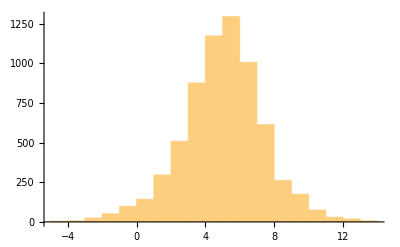

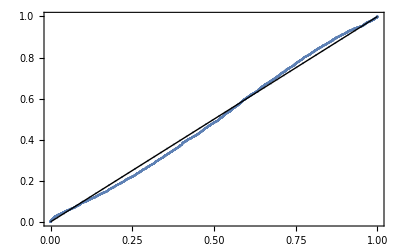

```mathematica
ts80modtemp="ts80mod";(*name of the group*)
Histogram@Log@DeleteCases[ToExpression@ts80modtemp,""]
ProbabilityPlot@Log@DeleteCases[ToExpression@ts80modtemp,""]
```

```mathematica
Kernel density estimation plots
```

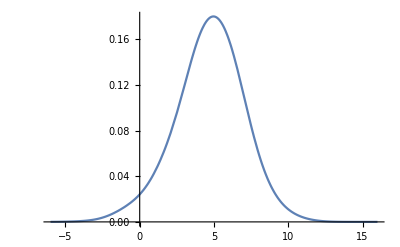

```mathematica
Plot[PDF[Fnip,x],{x,-6,16}]
```

```mathematica
Hypothesis tests
```

```mathematica
ts80modtemp1="ts80modtfs";
ts80modtemp2="ts80modtfm";(*name of the two groups*)
test1=Log@DeleteCases[ToExpression@ts80modtemp1,""];
test2=Log@DeleteCases[ToExpression@ts80modtemp2,""];
{{Mean[test1],Variance[test1],Dimensions[test1][[1]]},{Mean[test2],Variance[test2],Dimensions[test2][[1]]}}
chi2range=Solve[CDF[StudentTDistribution[Dimensions[test1]⟦1⟧+Dimensions[test2]⟦1⟧-2],x]==0.95,x][[1]];
mu=Solve[(Mean[test1]-Mean[test2]-y)/Sqrt[(((Dimensions[test1]⟦1⟧-1)*Variance[test1]+(Dimensions[test2]⟦1⟧-1)*Variance[test2])/(Dimensions[test1]⟦1⟧+Dimensions[test2]⟦1⟧-2))*(1/(Dimensions[test1]⟦1⟧)+1/(Dimensions[test2]⟦1⟧))]==x,y]/.chi2range
E^y/.mu
```

{{6.05299,8.11253,402},{4.57581,4.60779,3608}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{y→1.28455}}

{3.61306}

```mathematica
To give lists of test conditions and results of top 10 devices
```

```mathematica
ranking=1;
ts80modtemp="ts80mod";(*name of the group*)
index=Position[ToExpression@ts80modtemp,Union[ToExpression@ts80modtemp]⟦-1-ranking⟧]⟦1⟧
{Index[index+1,"Stability_time_total_exposure"],Index[index+1,"Stability_PCE_end_of_experiment"]}
ts80raw⟦index⟧
{temperature⟦index⟧,AFt⟦index⟧}
{humidity⟦index⟧,AFh⟦index⟧}
{illumination⟦index⟧,AFi⟦index⟧}
ts80mod⟦index⟧
Index[index+1,"Cell_stack_sequence"]
Index[index+1,"Perovskite_composition_short_form"]
Index[index+1,"Encapsulation"]
```

{5014}

{{1000},{94.7}}

{4097.67}

{{85.},{43.2805}}

{{85},{4.25}}

{{100},{1.}}

{753734.}

{SLG | FTO | TiO2-c | Perovskite | PCPD2FBT:BCF | PEDOT:PSS | ITO | SLG}

{FAMAPbBrI}

{TRUE}

```mathematica
To generate the final dataset with calculated values
```

```mathematica
datam=Join[data,{{"Tolerance factor"}}~Join~Transpose@{TolFac},{{"TS80"}}~Join~Transpose@{ts80raw},{{"Atemperature"}}~Join~Transpose@{AFtvalues},{{"Ahumidity"}}~Join~Transpose@{AFhvalues},{{"Alight"}}~Join~Transpose@{AFivalues},{{"TS80m"}}~Join~Transpose@{ts80mod},2];
```

```mathematica
Export["D:/Github/PSCstability/datam.csv",datam];
```